```mathematica
market = First[database];
td = TrendDuration[market["Prices"]];
```

```mathematica
PlotSequence[seq_]:=Manipulate[Part[seq,i],{i,1,Length[seq],1}];
```

```mathematica
HistogramPoints[data_]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data],1]];
HistogramPoints[data_,bspec_]:=Transpose[MapAt[Drop[#,1]&,HistogramList[data,bspec],1]];
HistogramPointPlot[data_,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
{pltData,pltData},
Joined->{False,True},
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{First[colors],{PointSize[Large],First[colors]}},
ImageSize->650,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
```

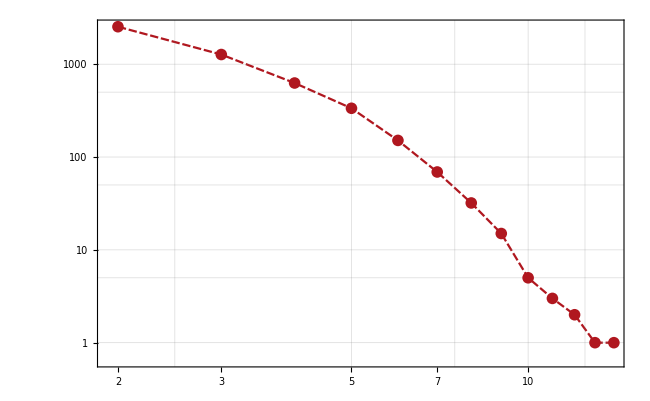

```mathematica
HistogramPointPlot[td,PlotRange->Full,ScalingFunctions->{"Log","Log"}]
```